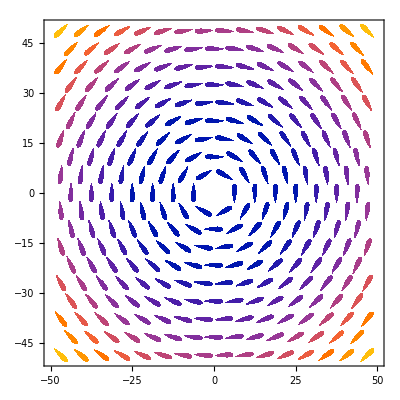

{-x_2 (x_1^2+x_2^2),x_1 (x_1^2+x_2^2)}

{x_1,x_2}

(-2 x_1 x_2 | -x_1^2-3 x_2^2
3 x_1^2+x_2^2 | 2 x_1 x_2)

```mathematica
(*This system is a center; hence, some solutions to linearization grows with time*)
VectorPlot[{-Subscript[x, 2] (Subscript[x, 1]^2+Subscript[x, 2]^2), Subscript[x, 1] (Subscript[x, 1]^2+Subscript[x, 2]^2)}, {Subscript[x, 1], -50, 50}, {Subscript[x, 2], -50, 50},VectorMarkers->"Drop"]


a = {-Subscript[x, 2] (Subscript[x, 1]^2+Subscript[x, 2]^2),Subscript[x, 1] (Subscript[x, 1]^2+Subscript[x, 2]^2)}
b = {Subscript[x, 1],Subscript[x, 2]}
D[a,{b}]//MatrixForm
```

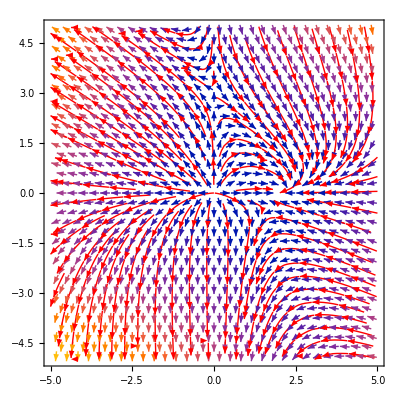

{{2-2 x_1-x_2,-x_1},{-2 x_2,3-2 x_1-2 x_2}}

```mathematica
StreamPlot[{2x-x^2+x*y, 3y-2x*y-y^2}, {x, -5, 5}, {y, -5,
   5}, VectorPoints -> 30,
 StreamColorFunction -> None,  StreamStyle -> {Black, Red}, ImageSize -> 400]


A={{2-2 Subscript[x, 1]-Subscript[x, 2],-Subscript[x, 1]},{-2 Subscript[x, 2],3-2 Subscript[x, 1]-2 Subscript[x, 2]}}
Eigenvalues[A]/.Subscript[x, 1]->0/.Subscript[x, 2]->0;
Eigenvectors[A]/.Subscript[x, 1]->0/.Subscript[x, 2]->0.00000001;

Eigenvalues[A]/.Subscript[x, 1]->0/.Subscript[x, 2]->3;
Eigenvectors[A]/.Subscript[x, 1]->0/.Subscript[x, 2]->3;

(*I could not locate fixed point (1,1) here*)
```

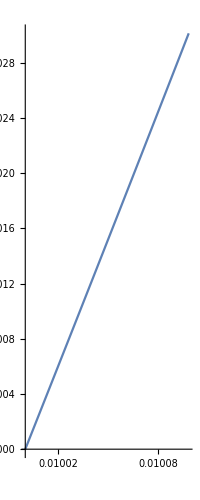

```mathematica
eq1:={x'[t]==x[t] - (x[t])^2-x[t] y[t],y'[t]==3y[t] - 2x[t] y[t] - (y[t])^2,y[0]==0.01,x[0]==0.01};
{xans1[t_],yans1[t_]}={x[t],y[t]}/.Flatten[NDSolve[eq1,{x[t],y[t]},{t,0,0,10}]];
ParametricPlot[{xans1[t], yans1[t]}, {t, 0, 0.01}]

(*It escapes pretty fast*)
```

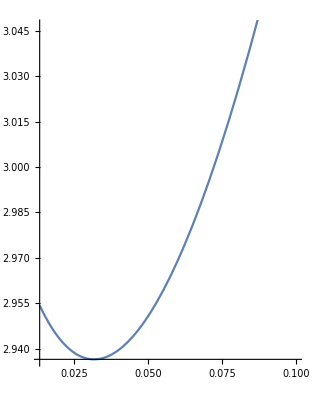

```mathematica
eq2:={x'[t]==x[t] - (x[t])^2-x[t] y[t],y'[t]==3y[t] - 2x[t] y[t] - (y[t])^2,x[0]==0.1,y[0]==3.1};
{xans2[t_],yans2[t_]}={x[t],y[t]}/.Flatten[NDSolve[eq2,{x[t],y[t]},{t,0,0,100}]];
ParametricPlot[{xans2[t], yans2[t]}, {t, 0, 1}]
```

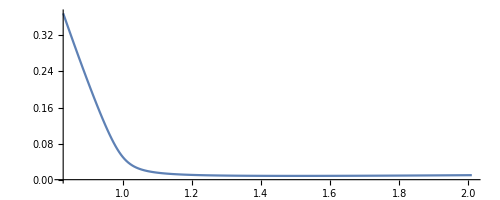

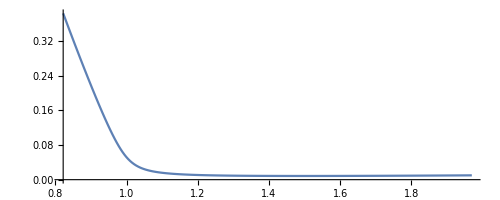

```mathematica
eq3a:={x'[t]==x[t] - (x[t])^2-x[t] y[t],y'[t]==3y[t] - 2x[t] y[t] - (y[t])^2,x[0]==2.01,y[0]==0.01};
{xans3a[t_],yans3a[t_]}={x[t],y[t]}/.Flatten[NDSolve[eq3a,{x[t],y[t]},{t,0,0,100}]];
ParametricPlot[{xans3a[t], yans3a[t]}, {t, 0, 5}]

eq3b:={x'[t]==x[t] - (x[t])^2-x[t] y[t],y'[t]==3y[t] - 2x[t] y[t] - (y[t])^2,x[0]==1.97,y[0]==0.01};
{xans3b[t_],yans3b[t_]}={x[t],y[t]}/.Flatten[NDSolve[eq3b,{x[t],y[t]},{t,0,0,100}]];
ParametricPlot[{xans3b[t], yans3b[t]}, {t, 0, 5}]

(* Pretty stable about the fixed point *)
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

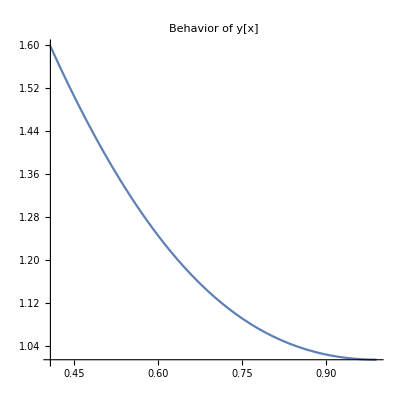

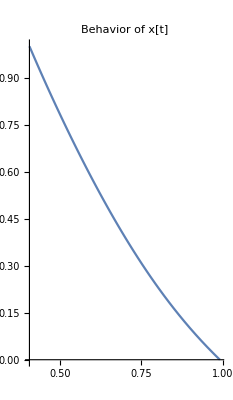

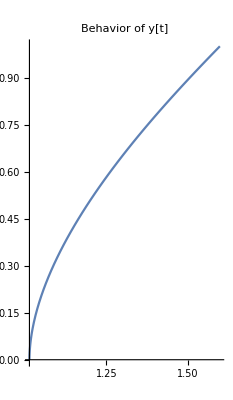

```mathematica
eq4a:={x'[t]==x[t] - (x[t])^2-x[t] y[t],y'[t]==3y[t] - 2x[t] y[t] - (y[t])^2,x[0]==0.99,y[0]==1.014};
{xans4a[t_],yans4a[t_]}={x[t],y[t]}/.Flatten[NDSolve[eq4a,{x[t],y[t]},{t,0,0,100}]]
ParametricPlot[{xans4a[t], yans4a[t]}, {t, 0, 1},PlotLabel->"Behavior of y[x]"]

ParametricPlot[{xans4a[t], t}, {t, 0, 1}, PlotLabel->"Behavior of x[t]"]
ParametricPlot[{yans4a[t], t}, {t, 0, 1},PlotLabel->"Behavior of y[t]"]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

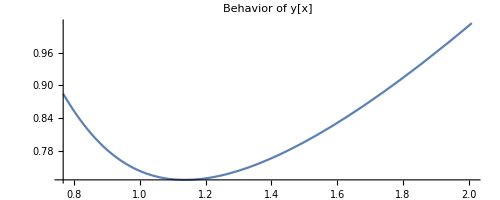

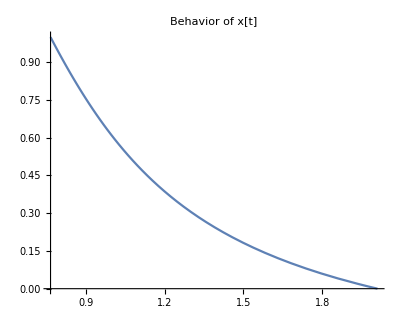

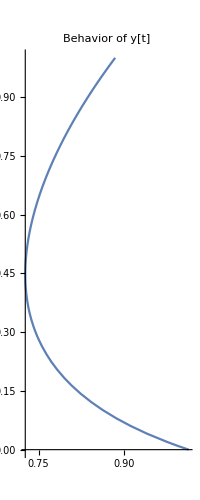

```mathematica
eq4b:={x'[t]==x[t] - (x[t])^2-x[t] y[t],y'[t]==3y[t] - 2x[t] y[t] - (y[t])^2,x[0]==2.01,y[0]==1.014};
{xans4b[t_],yans4b[t_]}={x[t],y[t]}/.Flatten[NDSolve[eq4b,{x[t],y[t]},{t,0,0,100}]]
ParametricPlot[{xans4b[t], yans4b[t]}, {t, 0, 1}, PlotLabel->"Behavior of y[x]"]
ParametricPlot[{xans4b[t], t}, {t, 0, 1}, PlotLabel->"Behavior of x[t]"]
ParametricPlot[{yans4b[t], t}, {t, 0, 1}, PlotLabel->"Behavior of y[t]"]

(* There is a radical difference between the behavior about the fixed point of two slightly different initial
value configuration *)
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

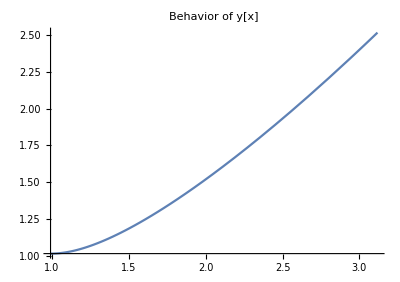

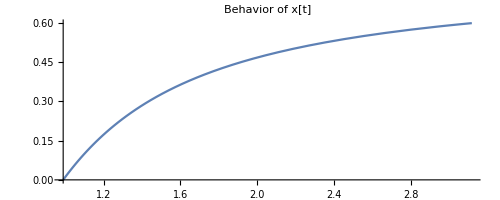

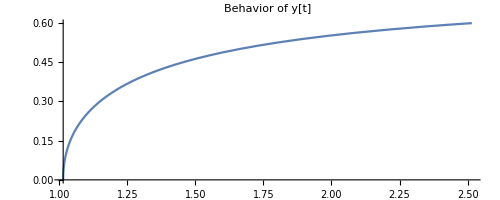

```mathematica
eq5a:={x'[t]==-(x[t] - (x[t])^2-x[t] y[t]),y'[t]==-(3y[t] - 2x[t] y[t] - (y[t])^2),x[0]==0.99,y[0]==1.014};
{xans5a[t_],yans5a[t_]}={x[t],y[t]}/.Flatten[NDSolve[eq5a,{x[t],y[t]},{t,0,0,0.6}]]

ParametricPlot[{xans5a[t], yans5a[t]}, {t, 0, 0.6},PlotLabel->"Behavior of y[x]"]
ParametricPlot[{xans5a[t], t}, {t, 0, 0.6}, PlotLabel->"Behavior of x[t]"]
ParametricPlot[{yans5a[t], t}, {t, 0, 0.6},PlotLabel->"Behavior of y[t]"]
```

```mathematica
eq5b:={x'[t]==-(x[t] - (x[t])^2-x[t] y[t]),y'[t]==-(3y[t] - 2x[t] y[t] - (y[t])^2),x[0]==0.99,y[0]==1.014};
{xans5b[t_],yans5b[t_]}={x[t],y[t]}/.Flatten[NDSolve[eq5b,{x[t],y[t]},{t,0,0,0.6}]]

ParametricPlot[{xans5b[t], yans5b[t]}, {t, 0, 0.6},PlotLabel->"Behavior of y[x]"]
ParametricPlot[{xans5b[t], t}, {t, 0, 0.6}, PlotLabel->"Behavior of x[t]"]
ParametricPlot[{yans5b[t], t}, {t, 0, 0.6},PlotLabel->"Behavior of y[t]"]

(*Backwards, the behavior is pretty much the same *)
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

-Graphics-

-Graphics-

-Graphics-